## Problem 1

```mathematica
in[m_,R_]:=m*R^2/2
```

## Problem 2

```mathematica
amu = 931.5*^6;
erot[l_,r_,a_]:=Module[{inertia},
l*(l+1)*(1240/(2π))^2/(2*(a*amu*r^2)/2)
]
erot[1,0.23,25]
```

0.0000632317

## Problem 3

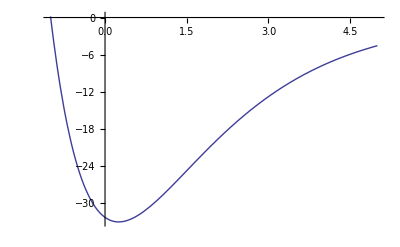

0.00825613

```mathematica
u[r_]:=33*((Exp[(0.25-r)/1.8]-1)^2-1)
Plot[u[r],{r,-1,5}]
data=Table[{r,u[r]},{r,.20,.30,.01}];
k = ki/.FindFit[data,-33+1/2*ki*(r-0.25)^2,ki,r][[1]];
√(k/((25*931.5*^6)/2))*1240/(2Pi)
```